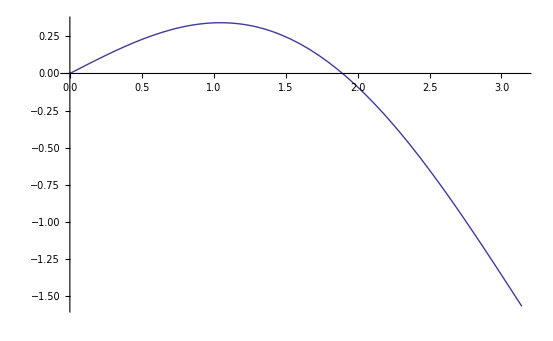
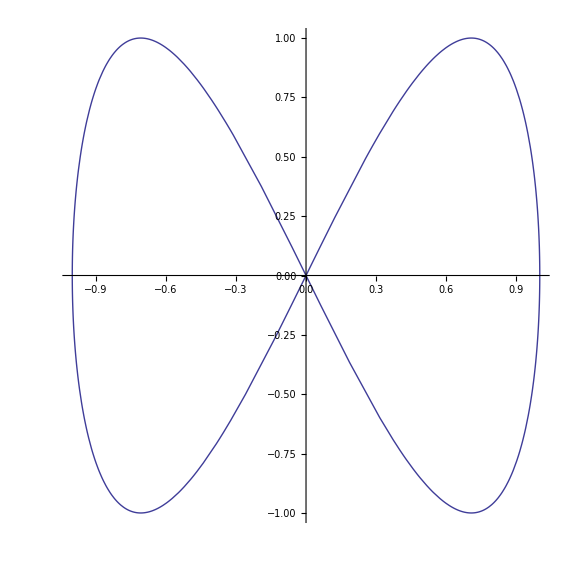
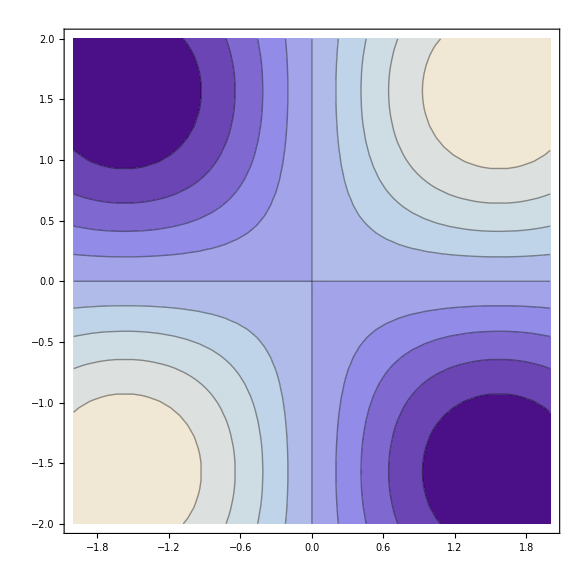
```mathematica
(* In this way you write comments *)
(* All commands with capital letters. Put ; at end of each line if you don't want printing on the screen *)
(* Clear all variables is a good thing to avoid problems *)
Clear["`*"];
(* Below I give the outprint after each command  or commands*)
a=Sqrt[2];
Print[a]
√2
(* calculate integral of x^2 from zero to Pi *)
Integrate[x^2,{x,0,Pi}]
π^3/3
(* Note the various forms of brackets *)
(* Defining a function f with _ and := *)
f[x_]:=Sin[x]-(x / 2);
Plot[f[x],{x,0,Pi}]
-Graphics-
(* Solving equations with Solve. Numerical solution with NSolve. For non-algebraic equations FindRoot is better. Here I am looking for a root near 1.9. Note == sign *)
FindRoot[f[x]==0,{x,1.9}]
{x->1.895494267033981}

(* Here is a function of three vaiables *)
g[x_,y_,z_]:=x^2 -2 y z + y + x z;
Print["g(1,2,3)=",g[1,2,3]]
"g(1,2,3)="-6

(* 3x 3 matrix A, row by row *)
a={{1,2,3},{2,5,6},{3,6,9}};
(* With these commands you get eigenvalues and eigenvectors *)
Eigenvalues[a]
Eigenvectors[a]
{1/2 (15+√185),1/2 (15-√185),0}
{{1/3,1/12 (-5+√185),1},{1/3,1/12 (-5-√185),1},{-3,0,1}}

(* You can store data in a Table or an Array *)
Table[i^2,{i,6}]
{1,4,9,16,25,36}

m=Table[i-j,{i,2},{j,2}];
m[[1,2]]
-1

(* Creates a vector p and a matrix a1. You can for example give them values. See programming below*) 
Array[p,5]
Array[a1,{2,4}]
{p[1],p[2],p[3],p[4],p[5]}
{{a1[1,1],a1[1,2],a1[1,3],a1[1,4]},{a1[2,1],a1[2,2],a1[2,3],a1[2,4]}}

(* Sum 1+ 1/4 +........+1/n^2 up to n=100. Out comes a numerical value due to N. N[1/3]=0.333333. Percent sign % means previous result *)
Sum[1/j^2,{j,1,100}];
N[%]
1.6349839001848927

(* Numerical integration of a double integral. *)
NIntegrate[x^2+y^2,{x,0,1},{y,0,1}]
0.6666666666666666

(* You have aleardy seen Plot. Other possibilities are ParametricPlot, Plot3D and ContourPlot *)
ParametricPlot[{Sin[t],Sin[2t]},{t,0,2Pi}]
-Graphics-
Plot3D[Sin[x y],{x,0,3},{y,0,3}]
-Graphics3D-
ContourPlot[Sin[x] Sin[ y],{x,-2,2},{y,-2,2}]
-Graphics-

(* At last some programming *)
(* Outprint of 2,4,6,8 *)
Print["even numbers between 2 to 8"];
Do[Print[i],{i,2,8,2}]
"even numbers between 2 to 8"
2
4
6
8




(* Outprint of even numbers 2-8 and odd 9-16 *)
Print["even numbers between 2 to 8 and odd between 9 to 16"];
Do[If[i<9,Print[i],Print[i-1]],{i,2,16,2}]

"even numbers between 2 to 8 and odd between 9 to 16"
2
4
6
8
9
11
13
15
(* While and For are also very useful *)
(* s=1+2+3+4+5 calculated with For and s=1+2+3+4+5+6 with While*)

s=0;
For[i=1,i≤ 5,i++, s=s+i];
Print["s=",s]
"s="15

k=0;
s=0;
While[k< 6,
k=k+1;
 s=s+k];
Print["s=",s]
"s="21
```